# Earth Capture Rate Check

Flip Tanedo
flip.tanedo@ucr.edu
14 April 2017

Calculating the capture rate of dark matter (with dark photon mediators) in the Earth. 
For cross checking and extension of code in collaboration with Adam Green.

Please cite: 
https://arxiv.org/abs/1509.07525

Physics summary:
https://particlebites.com/?p=3370

## PREM Import

PREM import, from EarthChecker_v2.nb (Jan 2017):

The data about the density of the Earth comes from the PREM 500 model, available at PREM 500 from http://ds.iris.edu/ds/products/emc-prem/. The citations to this information are:

1. Dziewonski, A.M., and D.L. Anderson. 1981. “Preliminary reference Earth model.” Phys. Earth Plan. Int. 25:297-356.

2. Trabant, C., A. R. Hutko, M. Bahavar, R. Karstens, T. Ahern and R. Aster (2012), Data products at the IRIS DMC: stepping-stones for research and other application, Seismological Research Letters, 83(6), 846:854. doi: 10.1785/0220 120032

We make use of a file PREM500jordan.csv, which was processed by Jordan Smolinsky to remove duplicate entries. This file is assumed to be in the same directory as this notebook.

### Importing data and key features

```mathematica
myPath=NotebookDirectory[];
PREMlocation=myPath<>"PREM500jordan.csv";

RawPREMdata=Import[PREMlocation,"CSV"]; 
TempRadius=Transpose[RawPREMdata][[1]] m; 
TempDensity=Transpose[RawPREMdata][[2]] kg/m^3; 

Radius=TempRadius[[2;;]];
Density=TempDensity[[2;;]];
PREMlength=Length[Radius];

Rmeters=Radius/.m->1;
```

#### Sanity Check

```mathematica
TempRadius=Transpose[RawPREMdata][[1]] m; 
TempDensity=Transpose[RawPREMdata][[2]] kg/m^3; 

TempRadius[[1;;4]]
TempDensity[[1;;4]]

PREMlength
```

{0,12858 m,25716 m,38574 m}

{(13088.5 kg)/m^3,(13088.5 kg)/m^3,(13088.4 kg)/m^3,(13088.2 kg)/m^3}

491

### Shell Thicknesses and Shell Mass

Note that the shells are not evenly spaced in the PREM500 data.

```mathematica
ΔR=TempRadius[[2;;PREMlength+1]]-TempRadius[[1;;PREMlength]];
ΔRmeters=ΔR/.m->1;

ShellMass=4./3 π Density Radius^3-4./3 π  Density(Radius-ΔR)^3;
```

#### Sanity Check: Earth’s total density

This is supposed to match 5.972 e24 kg

```mathematica
4.π Radius^2 Density ΔR//Total
```

5.99058×10^24 kg

You get a more accurate estimate if you account for the curvature of the shell rather than taking the thin-shell approximation.

```mathematica
ShellMass[[2;;5]]
```

{8.15816×10^17 kg,2.21433×10^18 kg,4.31202×10^18 kg,7.10816×10^18 kg}

```mathematica
ShellMass[[1]]=1.165460137012716*^17 kg; (*kludge for weird bug with 0*)
(* I think Mathematica gets confused by the units on this one *)
ShellMass//Total
```

5.96874×10^24 kg

#### Sanity Check: Plot of Mass in Each Shell

```mathematica
ListPlot[ShellMass/.{kg->1},
Frame->True,
FrameLabel->{radius index,"Mass in each Shell [kg]"}]
```

-Graphics-

### Enclosed Mass

```mathematica
EnclosedMass= Accumulate[ShellMass];
```

#### Check of Enclosed Mass

```mathematica
EnclosedMass[[1;;4]] 
ListPlot[EnclosedMass/.{kg->1},
Frame->True,
FrameLabel->{radius index,"Mass enclosed by Shell [kg]"}]
```

{1.16546×10^17 kg,9.32362×10^17 kg,3.14669×10^18 kg,7.45871×10^18 kg}

-Graphics-

## Escape Velocity

The escape velocity in natural units is given by an integral over the enclosed mass M(s).

v^2=∫_r^∞ (2G M(s))/(s^2 c^2)ⅆs  (* [G]= L^3/(M T^2); c = speed of light *)

So to do this as an array we break apart the integral into two parts depending on whether one is inside or outside the radius of the Earth, R_max.

v(r)^2=∫_r^R_max (2G M(s))/(s^2 c^2)ⅆs +∫_R_max^∞ (2G M(R_max))/(s^2 c^2)ⅆs 
=(2 G)/c^2[(∑_(s=r)^R_max (M(s))/s^2 ΔR) +(M(R_max))/R_max]

We use the Accumulate command to take care of the first term. We don’t actually ask about r>R_max, so we can ignore the second term.

```mathematica
GN=6.67384 10^-11 m^3/(kg s^2) /.{kg->1000g,m->100 cm};
c=3. 10^10 cm/s;
v2=2 GN/c^2(ΔR Reverse[Accumulate[Reverse[EnclosedMass/Radius^2]]]+EnclosedMass[[Length[EnclosedMass]]]/Radius[[Length[Radius]]])/.{kg->1000 g,m->100 cm};
```

#### Sanity Checks

```mathematica
v2[[1;;4]]
```

{2.47019×10^-9,2.47017×10^-9,2.47015×10^-9,2.47011×10^-9}

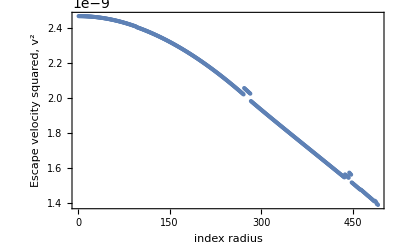

```mathematica
ListPlot[v2,
Frame->True,
FrameLabel->{radius index,"Escape velocity squared, v^2"}
]
```

We can redraw the above plot for actual radius, rather than “radius array index.”

```mathematica
RadiusAndEscVel2=Transpose[{Radius,v2}];
RadiusAndEscVel2[[1;;4]]
```

{{12858 m,2.47019×10^-9},{25716 m,2.47017×10^-9},{38574 m,2.47015×10^-9},{51432 m,2.47011×10^-9}}

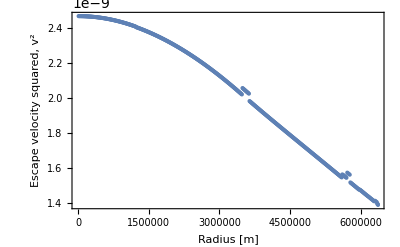

```mathematica
ListPlot[RadiusAndEscVel2/.{m->1},
Frame->True,
FrameLabel->{"Radius [m]","Escape velocity squared, v^2"}
]
```

## Load Data: Crust vs. Mantle

The data for the elemental mass fractions are from https://arxiv.org/abs/astro-ph/0401113:

-Graphics-

```mathematica
Elements = {
(* symbol, Z, A, Core, Mantle *)
{"O", 8, 16, 0, .44},
{"Si", 14, 28, .06,.21},
{"Mg",12,24,0,.228},
{"Fe",26,56,0.855,.0626},
{"Ca",20,40,0,.0253},
{"P",15,30,0.002,.00009},
{"Na",11,23,0,.0027},
{"S",16,32,0.019,.00025},
{"Ni",28,59,0.052,.00196},
{"Al",13,27,0,.0235},
{"Cr",24,52,0.009,.0026}
};
```

#### Sanity Check

```mathematica
%//MatrixForm
```

(O | 8 | 16 | 0 | 0.44
Si | 14 | 28 | 0.06 | 0.21
Mg | 12 | 24 | 0 | 0.228
Fe | 26 | 56 | 0.855 | 0.0626
Ca | 20 | 40 | 0 | 0.0253
P | 15 | 30 | 0.002 | 0.00009
Na | 11 | 23 | 0 | 0.0027
S | 16 | 32 | 0.019 | 0.00025
Ni | 28 | 59 | 0.052 | 0.00196
Al | 13 | 27 | 0 | 0.0235
Cr | 24 | 52 | 0.009 | 0.0026)

## Elemental Distribution

The core--mantle separator is r=3480 km. This corresponds to element 271 of 491.

```mathematica
Rcore=Radius[[271]];
Rearth=Radius[[491]];
```

### Reprocess elemental data

Column 5 is a little tricky, but it gives the number density of the element for each radial slice. The expression is:

n_i=(Mass Density in Shell)(mass fraction of element)1/(mass of element)[convert to 1/cm^3]

```mathematica
MyElements={
(*1*)#[[1]] (*name*),
(*2*)#[[2]] (*Z*),
(*3*)#[[3]] (*A*),
(*4*)#[[3]] .938272 GeV (* mass in GeV *),
(*5*) (Density  (* density of shell *)
Join[
Table[#[[4]],{271}], (* const Subscript[mass, i]/(total mass) for Subscript[r, i] in core *)
Table[#[[5]],{Length[Radius]-271}] (* const Subscript[mass, i]/(total mass) for Subscript[r, i] in mantle *)
] )/(#[[3]] .938272 GeV (*Subscript[m, proton]*) ) /.{kg->1000 g}/.{g->5.62 10^23 GeV}/.{m->100 cm}
(* list of Subscript[n, i] for each radius: ρ(mass frac)/mass =ρ Subscript[n, i]/(total mass density) *)
}&/@Elements;

mn=#[[4]]&/@MyElements; 
mnInGeV=mn/.GeV->1;

numberdensity=#[[5]]&/@MyElements; 
nmeters=numberdensity/.cm->10^-2;

Z=#[[2]]&/@MyElements;
```

#### Additional Discussion (what’s going on in column 5?)

Here’s how the Table commands work:

```mathematica
Table[#,{3}]&/@{aa,bb,cc,dd}
```

{{aa,aa,aa},{bb,bb,bb},{cc,cc,cc},{dd,dd,dd}}

The Join[...] command is creating an array whose first 271 elements are the core mass fraction, and the remaining elements are the mantle mass fraction.

#### Sanity Check

```mathematica
ListPlot[{MyElements[[11]][[5]],MyElements[[5]][[5]]}/.cm->1,
Frame->True,
FrameLabel->{"radius index","n_i [cm^-3]"}
]
```

-Graphics-

## Dark Matter Velocity Distribution

Start with galactic center rest frame velocity distribution. Eq. 17 of 1509.07525 (Earth paper). We’ll write all of our velocities in natural units. This simplifies units, but also has the benefit of making the velocity integral go over a finite range, which may help with the numerical integration.

### Basic Velocity Distribution

```mathematica
vgal=550 km/s/c /.{km->100000 cm}; (* galactic escape velocity *)
k=2.5; (* index parameter *)
u0=245 km/s/c /.{km->100000 cm}; 

(* Normalization *)
N0=NIntegrate[(E^((vgal^2-u^2)/(k u0^2))-1)^k 4π u^2 UnitStep[vgal-u],{u,0,1}];
f0[u_] :=1/N0(E^((vgal^2-u^2)/(k u0^2))-1)^k UnitStep[vgal-u]

(* assume full velocity distribution f[u] is the basic one *)
f[u_]:=f0[u];
```

#### Check

```mathematica
N0
```

2.29995×10^-7

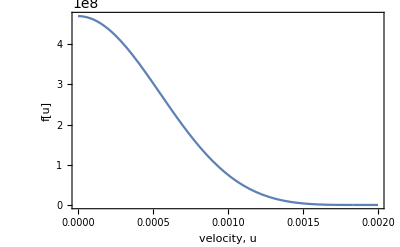

```mathematica
Plot[f[u],{u,0,.002},
Frame->True,
FrameLabel->{"velocity, u","f[u]"}]
```

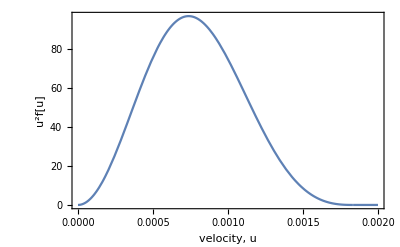

```mathematica
Plot[u^2 f[u] ,
{u,0,.002}, 
Frame->True,
FrameLabel->{"velocity, u","u^2f[u]"}]
```

### In progress: angular averaged velocity distribution

See equation16 of 1509.07525 (Earth paper). The observed dark matter velocity distribution in the Earth’s rest frame (which is our lab frame) is more complicated:

f[u]=1/4∫_-1^1 ⅆcosθ∫_-1^1 ⅆcosϕ f0[√(u^2+(V_sun+V_earth cos ϕ)^2+2u(V_sun+V_earth cos ϕ)cosθ)]
V_sun=220 km/s
V_earth=29.8 km/s

The reference is: hep-ph/9802253, but a better one is: T.S. Kosmas and J.D. Vergados, Phys. Rev. D 55, 1752 (1997).

A more pedagogical discussion may be section 2 of Lewin and Smith, “Review of Mathematics, Numerical Factors, and Corrections for Dark Matter Experiments Based on Elastic Nuclear Recoil”, Astropart.Phys. 6 (1996) 87-112.

```mathematica
Vsun=220 km/s/c /.{km->100000 cm};
Vearth=29.8 km/s/c /.{km->100000 cm};
favg[u_]:=1/4. NIntegrate[f0[√(u^2+(Vsun+Vearth cosϕ)^2+2u(Vsun+Vearth cosϕ)cosθ)],
{cosθ,-1,1},{cosϕ,-1,1}]
```

## Capture Rate

### Discussion

In order to perform the integral in (15), there are a couple of useful things to do:

(1) cancel the w^2dependence in dσ/dEr with the w^2 in the du integral coming from the distortion of the velocity distribution from the Earth’s gravitational potential.

(2) pull out common factors of ϵ^2 α_X n_X from C_cap since these are overall prefactors.

The resulting integral is:

(C^N)_cap=ϵ^2 α_X n_X(C^N)_(cap,red)
(C^N)_(cap,red)=∫_0^R ⅆ r4πr^2 n_N(r) ∫_0^c ⅆu 4π u f(u) ∫_E_min^E_max ⅆ E_R (8π α Z[n]^2 m[n])/((2m[n]E_R+mA^2)^2)F[n,E_R]^2
Emin=1/2 mX(w^2-(v_+[r])^2)=1/2 mX u^2
Emax = (2 μ^2)/mn w^2=2(mn mX^2)/(mn+mX)^2(u^2+v_esc[r]^2)

The integrand depends on:
- n=N, the nucleus
- the integration variables
- dark matter mass (in reduced mass)
- dark photon mass

Important remark: not explicitly shown: a Θ function that enforces E_max>E_min.

Notes on units: 
The integral over the earth radius is done in meters. 
The integral over the DM velocity is done in natural units (dimensionless velocities)
The integral over the recoil energy is done in GeV.

The final expression for (C^N)_(cap,red) is in 1/GeV^2. Upon multiplying by n_X this has units of 1/(GeV^2 cm^3) which we convert into 1/sec.

### Further Discussion: accounting for the range of asymptotic velocities

The integrand contains a factor (2m[n]E_R+mA^2)^-2. 

Observe that in the integration range, the E_R-dependent term is always subdominant. This is because we are restricted to the range where E_max>E_min. This implies that we are only sampling very small values of the asymptotic dark matter velocity, u.

Thus we may approximate:

1/((2m[n]E_R+mA^2)^2)=1/mA^4(1+2(2m[n]E_R)/mA^2+O((2m[n]E_R)/mA^2)^2)

Similarly, the Helm form factor is negligible because the momentum transfer is always small. This gives us:

(C^N)_(cap,red)=∫_0^R ⅆ r4πr^2 n_N(r) ∫_0^c ⅆu 4π u f(u) ∫_E_min^E_max ⅆ E_R (8π α Z[n]^2 m[n])/mA^4

=∫_0^R ⅆ r4πr^2 n_N(r) ∫_0^c ⅆu 4π u f(u) ×  (8π α Z[n]^2 m[n])/mA^4 (E_max-E_min) Θ(E_max-E_min)

(C^N)_cap=∫_0^R ⅆ r4πr^2 n_N(r) ∫_0^c ⅆu 4π u f(u) ×  (8π α Z[n]^2 m[n])/mA^4 (E_max-E_min) Θ(E_max-E_min)

### Revised capture rate

(C^N)_cap=ϵ^2 α_X n_X(8π α Z[n]^2 m[n])/mA^4∫_0^R ⅆ r4πr^2 n_N(r) ∫_0^c ⅆu 4π u f(u) (E_max(u)-E_min(u)) Θ(E_max-E_min)

Emin=1/2 mX(w^2-(v_+[r])^2)=1/2 mX u^2
Emax = (2 μ^2)/mn w^2=2(mn mX^2)/(mn+mX)^2(u^2+v_esc[r]^2)

We can improve this by setting an upper limit on the velocity integral. Recall that

Emin = a u^2
Emax = b u^2+c

These match at:
u_max=√(c/(a-b))=√((2 μ^2/mn v_esc[r]^2)/(1/2 mX-2 μ^2/mn))=v_esc[r]/(√(1/4(mX mn)/μ^2-1))=(2 v_esc[r])/(√((mX mn)/μ^2-4))=(2 v_esc[r])/(√((mX +mn)^2/(mX mn)-4))

This value of u_max is the upper limit of the velocity integral. Imposing this also obviates the Θ(E_max-E_min) factor.

With this:

(C^N)_cap=ϵ^2 α_X n_X(8π α Z[n]^2 mn)/mA^4∫_0^R ⅆ r4πr^2 n_N(r) ∫_0^u_max ⅆu 4π u f(u) (E_max(u)-E_min(u)) 
=ϵ^2 α_X n_X(8π α Z[n]^2 mn)/mA^4∫_0^R ⅆ r4πr^2 n_N(r) ∫_0^u_max ⅆu 4π u f(u) [2(mn mX^2)/(mn+mX)^2(u^2+v_esc[r]^2)-1/2 mX u^2]
=8π ϵ^2 α α_X n_X Z[n]^2 (mn mX)/mA^4∫_0^R ⅆ r4πr^2 n_N(r) ∫_0^u_max ⅆu 4π u f(u) [2 μ^2/(mn mX)(u^2+v_esc[r]^2)-1/2 u^2]

```mathematica
umax[rindex_,n_,mXinGeV_]:=2 √(v2[[rindex]]/((mXinGeV+mnInGeV[[n]])^2/(mXinGeV mnInGeV[[n]])-4))
uIntegrand[u_,rindex_,n_,mXinGeV_]:= 4π u f[u] ((2 (mnInGeV[[n]] mXinGeV)/(mnInGeV[[n]] +mXinGeV)^2)(u^2+v2[[rindex]])-1/2 u^2)
```

```mathematica
(* r integral is in meters, ΔR is included; the integrand is dimensionless *)
rIntegrand[rindex_,n_,mXinGeV_]:= 4π Rmeters[[rindex]]^2 ΔRmeters[[rindex]] nmeters[[n]][[rindex]]NIntegrate[uIntegrand[u,rindex,n,mXinGeV],{u,0,umax[rindex,n,mXinGeV]}]

rIntegrands[n_,mXinGeV_]:= rIntegrand[#,n,mXinGeV]&/@Range[Length[Radius]]

Ccap[ϵ_,αX_,n_,mXinGeV_,mAinGeV_]:=Total[8π ϵ^2 1/137. αX (0.3/mXinGeV (*1/cm^3*)) Z[[n]]^2(mnInGeV[[n]] mXinGeV)/mAinGeV^4(*1/GeV^2*)rIntegrands[n,mXinGeV] (1.98 10^-14 (*cm GeV*))^2(3 10^10 (*cm/s*))] 1/sec
```

#### Testing, takes 10 seconds

```mathematica
Timing[rIntegrands[1,1000.]]
```

{6.41659,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.16007×10^36,2.16774×10^36,2.17483×10^36,2.18216×10^36,2.1897×10^36,2.19668×10^36,2.20414×10^36,2.21103×10^36,2.21814×10^36,2.22548×10^36,2.23224×10^36,2.01915×10^36,2.0249×10^36,2.03088×10^36,2.03631×10^36,2.04195×10^36,2.04756×10^36,2.05313×10^36,2.05892×10^36,2.06417×10^36,2.06963×10^36,2.07505×10^36,2.08043×10^36,2.08603×10^36,2.09108×10^36,2.09634×10^36,2.10157×10^36,2.10702×10^36,2.1119×10^36,2.11701×10^36,2.12208×10^36,2.1271×10^36,2.13235×10^36,2.13703×10^36,2.14193×10^36,2.14679×10^36,2.15161×10^36,2.15664×10^36,2.16112×10^36,2.1658×10^36,2.17045×10^36,2.17506×10^36,2.17988×10^36,2.18413×10^36,2.18861×10^36,2.19304×10^36,2.19742×10^36,2.20202×10^36,2.20605×10^36,2.21031×10^36,2.21451×10^36,2.21893×10^36,2.22278×10^36,2.22685×10^36,2.23087×10^36,2.23485×10^36,2.23904×10^36,2.24265×10^36,2.24649×10^36,2.25027×10^36,2.25401×10^36,2.25797×10^36,2.26135×10^36,2.26494×10^36,2.26849×10^36,2.27199×10^36,2.2757×10^36,2.27884×10^36,2.28219×10^36,2.28549×10^36,2.28874×10^36,2.29221×10^36,2.2951×10^36,2.2982×10^36,2.30125×10^36,2.30452×10^36,2.30721×10^36,2.31011×10^36,2.31296×10^36,2.31576×10^36,2.31876×10^36,2.32119×10^36,2.32384×10^36,2.32643×10^36,2.32897×10^36,2.33171×10^36,2.33389×10^36,2.33627×10^36,2.3386×10^36,2.34087×10^36,2.34335×10^36,2.34526×10^36,2.34738×10^36,2.34944×10^36,2.35145×10^36,2.35366×10^36,2.3553×10^36,2.35715×10^36,2.35894×10^36,2.36067×10^36,2.36261×10^36,2.36398×10^36,2.36556×10^36,2.36707×10^36,2.36879×10^36,2.36994×10^36,2.37129×10^36,2.37259×10^36,2.37383×10^36,2.37527×10^36,2.37614×10^36,2.37721×10^36,2.37823×10^36,2.37919×10^36,2.38034×10^36,2.38094×10^36,2.38173×10^36,2.38246×10^36,2.38314×10^36,2.38401×10^36,2.38431×10^36,2.38482×10^36,2.38527×10^36,2.38566×10^36,2.38624×10^36,2.38627×10^36,2.38649×10^36,2.38665×10^36,2.387×10^36,2.3868×10^36,2.38678×10^36,2.38671×10^36,2.38658×10^36,2.38664×10^36,2.38615×10^36,2.38584×10^36,2.38548×10^36,2.38506×10^36,2.38483×10^36,2.38405×10^36,2.38345×10^36,2.3828×10^36,2.38209×10^36,2.38155×10^36,2.38049×10^36,2.3796×10^36,2.37865×10^36,2.37764×10^36,2.37682×10^36,2.37546×10^36,2.37428×10^36,2.37304×10^36,2.37197×10^36,2.37038×10^36,2.36896×10^36,2.36749×10^36,2.36595×10^36,2.36459×10^36,2.3627×10^36,2.36099×10^36,2.35923×10^36,2.3574×10^36,2.35573×10^36,2.35356×10^36,2.35156×10^36,2.7198×10^36,2.71693×10^36,2.71444×10^36,2.7114×10^36,2.70873×10^36,2.70552×10^36,2.70267×10^36,3.1174×10^36,3.11783×10^36,3.11817×10^36,3.11841×10^36,2.24391×10^36,2.23614×10^36,2.22793×10^36,2.21987×10^36,2.21195×10^36,2.20359×10^36,2.19538×10^36,2.18731×10^36,2.17881×10^36,2.17045×10^36,2.16224×10^36,2.1536×10^36,2.14511×10^36,2.13674×10^36,2.12798×10^36,2.10849×10^36,2.10454×10^36,2.10056×10^36,2.0967×10^36,2.09247×10^36,2.08836×10^36,2.08422×10^36,2.08004×10^36,2.07582×10^36,2.07172×10^36,2.06726×10^36,2.06292×10^36,2.05855×10^36,2.03832×10^36,2.03975×10^36,2.04115×10^36,2.04252×10^36,2.04385×10^36,2.04515×10^36,2.04641×10^36,2.04763×10^36,2.04882×10^36,2.04999×10^36,2.74253×10^36,2.74465×10^36,2.74638×10^36,1.18139×10^36,1.35546×10^36,1.32192×10^35}}

### Helm Form Factor

I believe this is completely negligible since E_r<< GeV .

```mathematica
Fn2[Er_ (*in GeV*),n_]:=
Module[{
En=0.114/(MyElements[[n]][[3]])^(5/3)},
E^(-Er/En)
]
```

#### Sanity Check

```mathematica
Fn2[.001 (*Er in GeV*),1 (*MyElements index*)] 

(*Edit by Adam Green 3/13/17*)(* Check: 0.4101745326788613 *)
```

0.410175

```mathematica
Fn2[.000001 (*Er in GeV*),1 (*MyElements index*)]
```

0.999109

## Test

```mathematica
Ccap[10^-8,0.035,4 (*Fe*),1000,1]
```

(2.48401×10^8)/sec